```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mkirk/Documents/bhabha_bsm

## Numerics

```mathematica
SMnumerics = {MZ2->(91.1876 GeV)^2,S->(240 GeV)^2,Alfa->1/128,Alfa2->1/128^2,cw->Sqrt[1-0.231],sw->Sqrt[0.231]};
BSMnumerics = {MZprime->5000 GeV, gZprimeL->0, gZprimeR->1, Mscalar->3500 GeV, gNP->1};
```

```mathematica
luminosity = 10/attobarns * (10^6 attobarns)/picobarns* (1 picobarns)/(2.568*^-9 GeV^-2)
```

3.89408×10^15 GeV^2

```mathematica
smallAngleBins = Range[0.064, 0.086,(0.086-0.064)/5]
smallAngleBinCentres = MovingAverage[smallAngleBins,2]
```

{0.064,0.0684,0.0728,0.0772,0.0816,0.086}

{0.0662,0.0706,0.075,0.0794,0.0838}

```mathematica
largeAngleBins = Range[π/4,3π/4,(π/2)/50]//N
largeAngleBinCentres = MovingAverage[largeAngleBins,2]
```

{0.785398,0.816814,0.84823,0.879646,0.911062,0.942478,0.973894,1.00531,1.03673,1.06814,1.09956,1.13097,1.16239,1.19381,1.22522,1.25664,1.28805,1.31947,1.35088,1.3823,1.41372,1.44513,1.47655,1.50796,1.53938,1.5708,1.60221,1.63363,1.66504,1.69646,1.72788,1.75929,1.79071,1.82212,1.85354,1.88496,1.91637,1.94779,1.9792,2.01062,2.04204,2.07345,2.10487,2.13628,2.1677,2.19911,2.23053,2.26195,2.29336,2.32478,2.35619}

{0.801106,0.832522,0.863938,0.895354,0.92677,0.958186,0.989602,1.02102,1.05243,1.08385,1.11527,1.14668,1.1781,1.20951,1.24093,1.27235,1.30376,1.33518,1.36659,1.39801,1.42942,1.46084,1.49226,1.52367,1.55509,1.5865,1.61792,1.64934,1.68075,1.71217,1.74358,1.775,1.80642,1.83783,1.86925,1.90066,1.93208,1.9635,1.99491,2.02633,2.05774,2.08916,2.12058,2.15199,2.18341,2.21482,2.24624,2.27765,2.30907,2.34049}

```mathematica
addNoise[central_,fractionalError_]:= With[{centralData=RandomVariate[NormalDistribution[central,central*fractionalError]]},
Around[centralData,RandomVariate[UniformDistribution[{0.8,1.2}*centralData*fractionalError]]]
]
```

## NP expressions

### Z prime

```mathematica
dσdΩZprime=1/(64 π^2 S)(((1+cos)^2 S^2 (4 cw^2 (gZprimeL^2-gZprimeR^2) (MZ2-S) (2 MZ2+S-cos S) (-4 MZprime^2+S+cos S) sw^2+Alfa π (MZprime^2-S) (2 MZprime^2+S-cos S) (-4 MZ2+S+cos S) (cw^4-2 cw^2 sw^2-3 sw^4))^2)/(8 cw^4 (MZ2-S)^2 (MZprime^2-S)^2 (2 MZ2+S-cos S)^2 (2 MZprime^2+S-cos S)^2 sw^4)+2 ((8 gZprimeL gZprimeR S)/(2 MZprime^2+S-cos S)-4 Alfa π (2/(-1+cos)+(S (cw^2-sw^2))/(cw^2 (2 MZ2+S-cos S))))^2+S^2 (-(gZprimeL-gZprimeR)^2/(MZprime^2-S)-(4 Alfa π)/(S-cos S)-(2 (gZprimeL^2+gZprimeR^2))/(2 MZprime^2+S-cos S)-(Alfa π (cw^2+sw^2)^2)/(4 cw^2 (MZ2-S) sw^2)-(Alfa π (cw^4-2 cw^2 sw^2+5 sw^4))/(2 cw^2 (2 MZ2+S-cos S) sw^2)) ((1+cos^2) (-(gZprimeL-gZprimeR)^2/(MZprime^2-S)-(4 Alfa π)/(S-cos S)-(2 (gZprimeL^2+gZprimeR^2))/(2 MZprime^2+S-cos S)-(Alfa π (cw^2+sw^2)^2)/(4 cw^2 (MZ2-S) sw^2)-(Alfa π (cw^4-2 cw^2 sw^2+5 sw^4))/(2 cw^2 (2 MZ2+S-cos S) sw^2))-2 cos ((gZprimeL+gZprimeR)^2/(MZprime^2-S)+(4 Alfa cos π)/(S-cos S)+(2 (gZprimeL^2+gZprimeR^2))/(2 MZprime^2+S-cos S)+(Alfa π (cw^2-3 sw^2)^2)/(4 cw^2 (MZ2-S) sw^2)+(Alfa π (cw^4-2 cw^2 sw^2+5 sw^4))/(2 cw^2 (2 MZ2+S-cos S) sw^2)))+S^2 ((gZprimeL+gZprimeR)^2/(MZprime^2-S)+(4 Alfa cos π)/(S-cos S)+(2 (gZprimeL^2+gZprimeR^2))/(2 MZprime^2+S-cos S)+(Alfa π (cw^2-3 sw^2)^2)/(4 cw^2 (MZ2-S) sw^2)+(Alfa π (cw^4-2 cw^2 sw^2+5 sw^4))/(2 cw^2 (2 MZ2+S-cos S) sw^2)) ((1+cos^2) ((gZprimeL+gZprimeR)^2/(MZprime^2-S)+(4 Alfa cos π)/(S-cos S)+(2 (gZprimeL^2+gZprimeR^2))/(2 MZprime^2+S-cos S)+(Alfa π (cw^2-3 sw^2)^2)/(4 cw^2 (MZ2-S) sw^2)+(Alfa π (cw^4-2 cw^2 sw^2+5 sw^4))/(2 cw^2 (2 MZ2+S-cos S) sw^2))+1/2 cos ((4 (gZprimeL-gZprimeR)^2)/(MZprime^2-S)+(16 Alfa π)/(S-cos S)+(8 (gZprimeL^2+gZprimeR^2))/(2 MZprime^2+S-cos S)+(Alfa π (cw^2+sw^2)^2)/(cw^2 (MZ2-S) sw^2)+(2 Alfa π (cw^4-2 cw^2 sw^2+5 sw^4))/(cw^2 (2 MZ2+S-cos S) sw^2))));
```

```mathematica
dσdΩZprime//FortranForm
```

(((1 + cos)**2*S**2*(4*cw**2*(gZprimeL**2 - gZprimeR**2)*(MZ2 - S)*(2*MZ2 + S - cos*S)*
     -           (-4*MZprime**2 + S + cos*S)*sw**2 + 
     -          Alfa*Pi*(MZprime**2 - S)*(2*MZprime**2 + S - cos*S)*(-4*MZ2 + S + cos*S)*
     -           (cw**4 - 2*cw**2*sw**2 - 3*sw**4))**2)/
     -     (8.*cw**4*(MZ2 - S)**2*(MZprime**2 - S)**2*(2*MZ2 + S - cos*S)**2*(2*MZprime**2 + S - cos*S)**2*
     -       sw**4) + 2*((8*gZprimeL*gZprimeR*S)/(2*MZprime**2 + S - cos*S) - 
     -        4*Alfa*Pi*(2/(-1 + cos) + (S*(cw**2 - sw**2))/(cw**2*(2*MZ2 + S - cos*S))))**2 + 
     -    S**2*(-((gZprimeL - gZprimeR)**2/(MZprime**2 - S)) - (4*Alfa*Pi)/(S - cos*S) - 
     -       (2*(gZprimeL**2 + gZprimeR**2))/(2*MZprime**2 + S - cos*S) - 
     -       (Alfa*Pi*(cw**2 + sw**2)**2)/(4.*cw**2*(MZ2 - S)*sw**2) - 
     -       (Alfa*Pi*(cw**4 - 2*cw**2*sw**2 + 5*sw**4))/(2.*cw**2*(2*MZ2 + S - cos*S)*sw**2))*
     -     ((1 + cos**2)*(-((gZprimeL - gZprimeR)**2/(MZprime**2 - S)) - (4*Alfa*Pi)/(S - cos*S) - 
     -          (2*(gZprimeL**2 + gZprimeR**2))/(2*MZprime**2 + S - cos*S) - 
     -          (Alfa*Pi*(cw**2 + sw**2)**2)/(4.*cw**2*(MZ2 - S)*sw**2) - 
     -          (Alfa*Pi*(cw**4 - 2*cw**2*sw**2 + 5*sw**4))/(2.*cw**2*(2*MZ2 + S - cos*S)*sw**2)) - 
     -       2*cos*((gZprimeL + gZprimeR)**2/(MZprime**2 - S) + (4*Alfa*cos*Pi)/(S - cos*S) + 
     -          (2*(gZprimeL**2 + gZprimeR**2))/(2*MZprime**2 + S - cos*S) + 
     -          (Alfa*Pi*(cw**2 - 3*sw**2)**2)/(4.*cw**2*(MZ2 - S)*sw**2) + 
     -          (Alfa*Pi*(cw**4 - 2*cw**2*sw**2 + 5*sw**4))/(2.*cw**2*(2*MZ2 + S - cos*S)*sw**2))) + 
     -    S**2*((gZprimeL + gZprimeR)**2/(MZprime**2 - S) + (4*Alfa*cos*Pi)/(S - cos*S) + 
     -       (2*(gZprimeL**2 + gZprimeR**2))/(2*MZprime**2 + S - cos*S) + 
     -       (Alfa*Pi*(cw**2 - 3*sw**2)**2)/(4.*cw**2*(MZ2 - S)*sw**2) + 
     -       (Alfa*Pi*(cw**4 - 2*cw**2*sw**2 + 5*sw**4))/(2.*cw**2*(2*MZ2 + S - cos*S)*sw**2))*
     -     ((1 + cos**2)*((gZprimeL + gZprimeR)**2/(MZprime**2 - S) + (4*Alfa*cos*Pi)/(S - cos*S) + 
     -          (2*(gZprimeL**2 + gZprimeR**2))/(2*MZprime**2 + S - cos*S) + 
     -          (Alfa*Pi*(cw**2 - 3*sw**2)**2)/(4.*cw**2*(MZ2 - S)*sw**2) + 
     -          (Alfa*Pi*(cw**4 - 2*cw**2*sw**2 + 5*sw**4))/(2.*cw**2*(2*MZ2 + S - cos*S)*sw**2)) + 
     -       (cos*((4*(gZprimeL - gZprimeR)**2)/(MZprime**2 - S) + (16*Alfa*Pi)/(S - cos*S) + 
     -            (8*(gZprimeL**2 + gZprimeR**2))/(2*MZprime**2 + S - cos*S) + 
     -            (Alfa*Pi*(cw**2 + sw**2)**2)/(cw**2*(MZ2 - S)*sw**2) + 
     -            (2*Alfa*Pi*(cw**4 - 2*cw**2*sw**2 + 5*sw**4))/(cw**2*(2*MZ2 + S - cos*S)*sw**2)))/2.))/
     -  (64.*Pi**2*S)

### New scalar

```mathematica
dσdΩScalar=(4 (-1+cos)^2 cos cw^4 gNP^4 (Mscalar^2-S) (MZ2-S)^2 S^2 ((1+cos) Mscalar^2-2 (-1+cos) S) (2 MZ2+S-cos S)^2 sw^4+Alfa2 (-1+cos)^2 (1+cos)^2 π^2 (Mscalar^2-S)^2 S^2 (2 Mscalar^2+S-cos S)^2 (-4 MZ2+S+cos S)^2 (cw^2-3 sw^2) (cw^2+sw^2) (cw^4-2 cw^2 sw^2-3 sw^4)+8 (MZ2-S)^2 sw^4 (1/2 (-1+cos) cw^2 gNP^2 (Mscalar^2-S) S (-2 MZ2+(-1+cos) S)+(-1+cos) cw^2 gNP^2 S (-2 Mscalar^2+(-1+cos) S) (-2 MZ2+(-1+cos) S)+8 Alfa cw^2 π (Mscalar^2-S) (-2 MZ2+(-1+cos) S) (2 Mscalar^2+S-cos S)+4 Alfa (-1+cos) π (Mscalar^2-S) S (-2 Mscalar^2+(-1+cos) S) (cw^2-sw^2)) (1/2 (-1+cos) cw^2 gNP^2 (Mscalar^2-S) S (-2 MZ2+(-1+cos) S)-1/2 (-1+cos) cos cw^2 gNP^2 (Mscalar^2-S) S (-2 MZ2+(-1+cos) S)+(-1+cos) cw^2 gNP^2 S (-2 Mscalar^2+(-1+cos) S) (-2 MZ2+(-1+cos) S)+8 Alfa cw^2 π (Mscalar^2-S) (-2 MZ2+(-1+cos) S) (2 Mscalar^2+S-cos S)+4 Alfa (-1+cos) π (Mscalar^2-S) S (-2 Mscalar^2+(-1+cos) S) (cw^2-sw^2))+2 (Mscalar^2-S)^2 (MZ2-S)^2 sw^4 (-((-1+cos) cw^2 gNP^2 S (-2 MZ2+(-1+cos) S))-8 Alfa π (2 Mscalar^2+S-cos S) (cw^2 (4 MZ2+S-cos S)-(-1+cos) S sw^2)) ((-1+cos)^2 cw^2 gNP^2 S (-2 MZ2+(-1+cos) S)-8 Alfa π (2 Mscalar^2+S-cos S) (cw^2 (4 MZ2+S-cos S)-(-1+cos) S sw^2))+8 (Mscalar^2-S)^2 (1/2 (-1+cos) cw^2 gNP^2 (MZ2-S) S (-2 MZ2+(-1+cos) S) sw^2+4 Alfa cw^2 π (MZ2-S) (-2 Mscalar^2+(-1+cos) S) (2 MZ2+S-cos S) sw^2+1/4 Alfa (-1+cos) π S (-2 Mscalar^2+(-1+cos) S) (cw^4 (-4 MZ2+S+cos S)+2 (-3+cos) cw^2 S sw^2+(-12 MZ2+(9+cos) S) sw^4)) ((1+cos^2) (1/2 (-1+cos) cw^2 gNP^2 (MZ2-S) S (-2 MZ2+(-1+cos) S) sw^2+4 Alfa cw^2 π (MZ2-S) (-2 Mscalar^2+(-1+cos) S) (2 MZ2+S-cos S) sw^2+1/4 Alfa (-1+cos) π S (-2 Mscalar^2+(-1+cos) S) (cw^4 (-4 MZ2+S+cos S)+2 (-3+cos) cw^2 S sw^2+(-12 MZ2+(9+cos) S) sw^4))+1/2 cos (-16 Alfa cos cw^2 π (MZ2-S) (-2 Mscalar^2+(-1+cos) S) (-2 MZ2+(-1+cos) S) sw^2+Alfa (-1+cos) π S (-2 Mscalar^2+(-1+cos) S) (-2 MZ2+(-1+cos) S) (cw^2-3 sw^2)^2-2 (1-cos) (MZ2-S) S (cw^2 gNP^2 (2 MZ2+S-cos S) sw^2+Alfa π (2 Mscalar^2+S-cos S) (cw^4-2 cw^2 sw^2+5 sw^4))))+8 (Mscalar^2-S)^2 (4 Alfa cos cw^2 π (MZ2-S) (-2 Mscalar^2+(-1+cos) S) (-2 MZ2+(-1+cos) S) sw^2-1/4 Alfa (-1+cos) π S (-2 Mscalar^2+(-1+cos) S) (-2 MZ2+(-1+cos) S) (cw^2-3 sw^2)^2+1/2 (1-cos) (MZ2-S) S (cw^2 gNP^2 (2 MZ2+S-cos S) sw^2+Alfa π (2 Mscalar^2+S-cos S) (cw^4-2 cw^2 sw^2+5 sw^4))) (-2 cos (1/2 (-1+cos) cw^2 gNP^2 (MZ2-S) S (-2 MZ2+(-1+cos) S) sw^2+4 Alfa cw^2 π (MZ2-S) (-2 Mscalar^2+(-1+cos) S) (2 MZ2+S-cos S) sw^2+1/4 Alfa (-1+cos) π S (-2 Mscalar^2+(-1+cos) S) (cw^4 (-4 MZ2+S+cos S)+2 (-3+cos) cw^2 S sw^2+(-12 MZ2+(9+cos) S) sw^4))+(1+cos^2) (4 Alfa cos cw^2 π (MZ2-S) (-2 Mscalar^2+(-1+cos) S) (-2 MZ2+(-1+cos) S) sw^2-1/4 Alfa (-1+cos) π S (-2 Mscalar^2+(-1+cos) S) (-2 MZ2+(-1+cos) S) (cw^2-3 sw^2)^2+1/2 (1-cos) (MZ2-S) S (cw^2 gNP^2 (2 MZ2+S-cos S) sw^2+Alfa π (2 Mscalar^2+S-cos S) (cw^4-2 cw^2 sw^2+5 sw^4)))))/(512 (-1+cos)^2 cw^4 π^2 (Mscalar^2-S)^2 (MZ2-S)^2 S (2 Mscalar^2+S-cos S)^2 (2 MZ2+S-cos S)^2 sw^4);
```

```mathematica
dσdΩScalar//FortranForm
```

(4*(-1 + cos)**2*cos*cw**4*gNP**4*(Mscalar**2 - S)*(MZ2 - S)**2*S**2*
     -     ((1 + cos)*Mscalar**2 - 2*(-1 + cos)*S)*(2*MZ2 + S - cos*S)**2*sw**4 + 
     -    Alfa2*(-1 + cos)**2*(1 + cos)**2*Pi**2*(Mscalar**2 - S)**2*S**2*(2*Mscalar**2 + S - cos*S)**2*
     -     (-4*MZ2 + S + cos*S)**2*(cw**2 - 3*sw**2)*(cw**2 + sw**2)*(cw**4 - 2*cw**2*sw**2 - 3*sw**4) + 
     -    8*(MZ2 - S)**2*sw**4*(((-1 + cos)*cw**2*gNP**2*(Mscalar**2 - S)*S*(-2*MZ2 + (-1 + cos)*S))/2. + 
     -       (-1 + cos)*cw**2*gNP**2*S*(-2*Mscalar**2 + (-1 + cos)*S)*(-2*MZ2 + (-1 + cos)*S) + 
     -       8*Alfa*cw**2*Pi*(Mscalar**2 - S)*(-2*MZ2 + (-1 + cos)*S)*(2*Mscalar**2 + S - cos*S) + 
     -       4*Alfa*(-1 + cos)*Pi*(Mscalar**2 - S)*S*(-2*Mscalar**2 + (-1 + cos)*S)*(cw**2 - sw**2))*
     -     (((-1 + cos)*cw**2*gNP**2*(Mscalar**2 - S)*S*(-2*MZ2 + (-1 + cos)*S))/2. - 
     -       ((-1 + cos)*cos*cw**2*gNP**2*(Mscalar**2 - S)*S*(-2*MZ2 + (-1 + cos)*S))/2. + 
     -       (-1 + cos)*cw**2*gNP**2*S*(-2*Mscalar**2 + (-1 + cos)*S)*(-2*MZ2 + (-1 + cos)*S) + 
     -       8*Alfa*cw**2*Pi*(Mscalar**2 - S)*(-2*MZ2 + (-1 + cos)*S)*(2*Mscalar**2 + S - cos*S) + 
     -       4*Alfa*(-1 + cos)*Pi*(Mscalar**2 - S)*S*(-2*Mscalar**2 + (-1 + cos)*S)*(cw**2 - sw**2)) + 
     -    2*(Mscalar**2 - S)**2*(MZ2 - S)**2*sw**4*
     -     (-((-1 + cos)*cw**2*gNP**2*S*(-2*MZ2 + (-1 + cos)*S)) - 
     -       8*Alfa*Pi*(2*Mscalar**2 + S - cos*S)*(cw**2*(4*MZ2 + S - cos*S) - (-1 + cos)*S*sw**2))*
     -     ((-1 + cos)**2*cw**2*gNP**2*S*(-2*MZ2 + (-1 + cos)*S) - 
     -       8*Alfa*Pi*(2*Mscalar**2 + S - cos*S)*(cw**2*(4*MZ2 + S - cos*S) - (-1 + cos)*S*sw**2)) + 
     -    8*(Mscalar**2 - S)**2*(((-1 + cos)*cw**2*gNP**2*(MZ2 - S)*S*(-2*MZ2 + (-1 + cos)*S)*sw**2)/2. + 
     -       4*Alfa*cw**2*Pi*(MZ2 - S)*(-2*Mscalar**2 + (-1 + cos)*S)*(2*MZ2 + S - cos*S)*sw**2 + 
     -       (Alfa*(-1 + cos)*Pi*S*(-2*Mscalar**2 + (-1 + cos)*S)*
     -          (cw**4*(-4*MZ2 + S + cos*S) + 2*(-3 + cos)*cw**2*S*sw**2 + (-12*MZ2 + (9 + cos)*S)*sw**4))/
     -        4.)*((1 + cos**2)*(((-1 + cos)*cw**2*gNP**2*(MZ2 - S)*S*(-2*MZ2 + (-1 + cos)*S)*sw**2)/2. + 
     -          4*Alfa*cw**2*Pi*(MZ2 - S)*(-2*Mscalar**2 + (-1 + cos)*S)*(2*MZ2 + S - cos*S)*sw**2 + 
     -          (Alfa*(-1 + cos)*Pi*S*(-2*Mscalar**2 + (-1 + cos)*S)*
     -             (cw**4*(-4*MZ2 + S + cos*S) + 2*(-3 + cos)*cw**2*S*sw**2 + (-12*MZ2 + (9 + cos)*S)*sw**4)
     -             )/4.) + (cos*(-16*Alfa*cos*cw**2*Pi*(MZ2 - S)*(-2*Mscalar**2 + (-1 + cos)*S)*
     -             (-2*MZ2 + (-1 + cos)*S)*sw**2 + 
     -            Alfa*(-1 + cos)*Pi*S*(-2*Mscalar**2 + (-1 + cos)*S)*(-2*MZ2 + (-1 + cos)*S)*
     -             (cw**2 - 3*sw**2)**2 - 2*(1 - cos)*(MZ2 - S)*S*
     -             (cw**2*gNP**2*(2*MZ2 + S - cos*S)*sw**2 + 
     -               Alfa*Pi*(2*Mscalar**2 + S - cos*S)*(cw**4 - 2*cw**2*sw**2 + 5*sw**4))))/2.) + 
     -    8*(Mscalar**2 - S)**2*(4*Alfa*cos*cw**2*Pi*(MZ2 - S)*(-2*Mscalar**2 + (-1 + cos)*S)*
     -        (-2*MZ2 + (-1 + cos)*S)*sw**2 - 
     -       (Alfa*(-1 + cos)*Pi*S*(-2*Mscalar**2 + (-1 + cos)*S)*(-2*MZ2 + (-1 + cos)*S)*
     -          (cw**2 - 3*sw**2)**2)/4. + ((1 - cos)*(MZ2 - S)*S*
     -          (cw**2*gNP**2*(2*MZ2 + S - cos*S)*sw**2 + 
     -            Alfa*Pi*(2*Mscalar**2 + S - cos*S)*(cw**4 - 2*cw**2*sw**2 + 5*sw**4)))/2.)*
     -     (-2*cos*(((-1 + cos)*cw**2*gNP**2*(MZ2 - S)*S*(-2*MZ2 + (-1 + cos)*S)*sw**2)/2. + 
     -          4*Alfa*cw**2*Pi*(MZ2 - S)*(-2*Mscalar**2 + (-1 + cos)*S)*(2*MZ2 + S - cos*S)*sw**2 + 
     -          (Alfa*(-1 + cos)*Pi*S*(-2*Mscalar**2 + (-1 + cos)*S)*
     -             (cw**4*(-4*MZ2 + S + cos*S) + 2*(-3 + cos)*cw**2*S*sw**2 + (-12*MZ2 + (9 + cos)*S)*sw**4)
     -             )/4.) + (1 + cos**2)*(4*Alfa*cos*cw**2*Pi*(MZ2 - S)*(-2*Mscalar**2 + (-1 + cos)*S)*
     -           (-2*MZ2 + (-1 + cos)*S)*sw**2 - 
     -          (Alfa*(-1 + cos)*Pi*S*(-2*Mscalar**2 + (-1 + cos)*S)*(-2*MZ2 + (-1 + cos)*S)*
     -             (cw**2 - 3*sw**2)**2)/4. + 
     -          ((1 - cos)*(MZ2 - S)*S*(cw**2*gNP**2*(2*MZ2 + S - cos*S)*sw**2 + 
     -               Alfa*Pi*(2*Mscalar**2 + S - cos*S)*(cw**4 - 2*cw**2*sw**2 + 5*sw**4)))/2.)))/
     -  (512.*(-1 + cos)**2*cw**4*Pi**2*(Mscalar**2 - S)**2*(MZ2 - S)**2*S*(2*Mscalar**2 + S - cos*S)**2*
     -    (2*MZ2 + S - cos*S)**2*sw**4)

### SM

```mathematica
(dσdΩZprime/.{gZprimeL->0, gZprimeR->0})==(dσdΩScalar/.{gNP->0})/.Alfa2->Alfa^2//Simplify
```

True

```mathematica
sm = dσdΩZprime/.{gZprimeL->0, gZprimeR->0}//Simplify;
```

```mathematica
sm//FortranForm
```

(Alfa**2*(512*(MZ2 - S)**2*sw**4*(cw**2*(4*MZ2 + S - cos*S) - (-1 + cos)*S*sw**2)**2 + 
     -      2*(-1 + cos)**2*(1 + cos)**2*S**2*(-4*MZ2 + S + cos*S)**2*
     -       (cw**4 - 2*cw**2*sw**2 - 3*sw**4)**2 + 
     -      ((-1 + cos)*cw**4*S*(-4*MZ2 + S + cos*S) + 
     -         2*cw**2*(16*MZ2**2 - 8*(1 + cos)*MZ2*S + (-5 + 4*cos + cos**2)*S**2)*sw**2 + 
     -         (-1 + cos)*S*(-12*MZ2 + (9 + cos)*S)*sw**4)*
     -       ((-1 + cos)*(1 + cos)**2*cw**4*S*(-4*MZ2 + S + cos*S) + 
     -         2*cw**2*(16*(1 + 3*cos**2)*MZ2**2 - 8*(1 + 3*cos + cos**2 + 3*cos**3)*MZ2*S + 
     -            (-5 + 2*cos - 12*cos**2 + 14*cos**3 + cos**4)*S**2)*sw**2 + 
     -         (-1 + cos)*S*(-4*(3 + 14*cos + 3*cos**2)*MZ2 + (9 + 3*cos + 27*cos**2 + cos**3)*S)*sw**4) + 
     -      ((-1 + cos)*cw**4*S*(-4*MZ2 + S + cos*S) - 
     -         2*cw**2*(cos**2*(8*MZ2 - 5*S)*S + S*(8*MZ2 + S) + 4*cos*(-4*MZ2**2 + S**2))*sw**2 + 
     -         (-1 + cos)*S*(-28*MZ2 + S + 9*cos*S)*sw**4)*
     -       ((-1 + cos)*(1 + cos)**2*cw**4*S*(-4*MZ2 + S + cos*S) - 
     -         2*cw**2*(cos**4*(8*MZ2 - 5*S)*S + 4*cos**2*(8*MZ2 - 3*S)*S + S*(8*MZ2 + S) + 
     -            2*cos**3*(-8*MZ2**2 + S**2) + cos*(-48*MZ2**2 + 16*MZ2*S + 14*S**2))*sw**2 + 
     -         (-1 + cos)*S*(-4*(7 + 6*cos + 7*cos**2)*MZ2 + (1 + 27*cos + 3*cos**2 + 9*cos**3)*S)*sw**4)))/
     -  (1024.*(-1 + cos)**2*cw**4*(MZ2 - S)**2*S*(2*MZ2 + S - cos*S)**2*sw**4)

## Small angle data generation

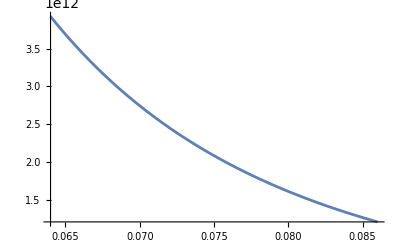

```mathematica
luminosity*sm/.SMnumerics/.cos->Cos[x];
Plot[%,{x,0.064,0.086}]
```

```mathematica
luminosity*sm/.SMnumerics/.cos->Cos[x]/.x->smallAngleBinCentres
smallAngleExpData = addNoise[#,1/1000]&/@%
```

{3.43109×10^12,2.65175×10^12,2.08155×10^12,1.65662×10^12,1.33474×10^12}

{3.43200.002810^12,2.64480.003210^12,2.08150.002210^12,1.65660.001410^12,1.33580.001610^12}

{{0.0662,3.43200.002810^12},{0.0706,2.64480.003210^12},{0.075,2.08150.002210^12},{0.0794,1.65660.001410^12},{0.0838,1.33580.001610^12}}

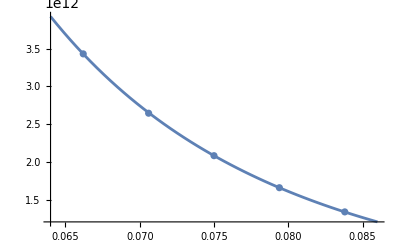

```mathematica
Transpose[{smallAngleBinCentres,smallAngleExpData}]
Show[
Plot[luminosity*sm/.SMnumerics/.cos->Cos[x],{x,Min[smallAngleBins],Max[smallAngleBins]}],
ListPlot[%]
]
```

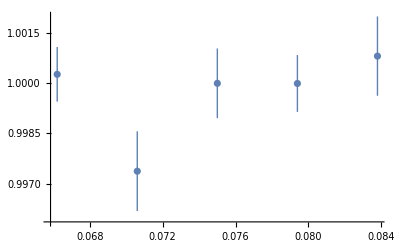

```mathematica
(luminosity*sm)/.SMnumerics/.cos->Cos[x]/.x->smallAngleBinCentres;
smallAngleExpData/%;
ListPlot[Transpose[{smallAngleBinCentres,%}]]
```

```mathematica
smallAngleBins//Length
```

6

```mathematica
Table[SetPrecision[{smallAngleBins[[i]],smallAngleBins[[i+1]],smallAngleExpData[[i]]["Value"]*(smallAngleBins[[i+1]]-smallAngleBins[[i]]),smallAngleExpData[[i]]["Uncertainty"]*(smallAngleBins[[i+1]]-smallAngleBins[[i]])},5], {i,1,Length[smallAngleBinCentres]}]
Export["small-angle-data.dat", %,"Table","FieldSeparators"->" ",Alignment->Left]
```

{{0.064,0.0684,1.5101×10^10,1.2304×10^7},{0.0684,0.0728,1.1637×10^10,1.389×10^7},{0.0728,0.0772,9.1588×10^9,9.5197×10^6},{0.0772,0.0816,7.289×10^9,6.1842×10^6},{0.0816,0.086,5.8776×10^9,6.9483×10^6}}

small-angle-data.dat

```mathematica
(luminosity*sm)/.SMnumerics/.cos->Cos[x]//Simplify;
Integrate[%,{x,0.064,0.0684}]
```

1.51526×10^10

## BSM Comparison

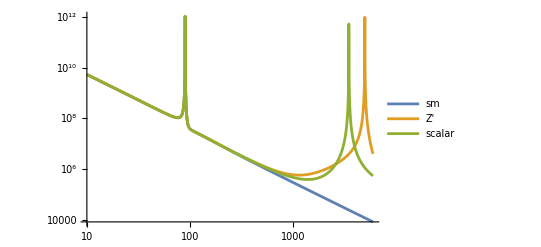

```mathematica
luminosity*{sm,dσdΩZprime,dσdΩScalar}/.S->sqrtS^2 GeV^2/.SMnumerics/.BSMnumerics/. cos->Cos[π/2]//Expand;
LogLogPlot[%,{sqrtS,10,6000},PlotLegends->{"sm","Z'","scalar"}]
```

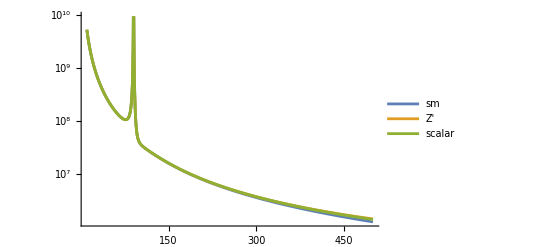

```mathematica
luminosity*{sm,dσdΩZprime,dσdΩScalar}/.S->sqrtS^2 GeV^2/.SMnumerics/.BSMnumerics/. cos->Cos[π/2]//Expand;
LogPlot[%,{sqrtS,10,500},PlotLegends->{"sm","Z'","scalar"}]
```

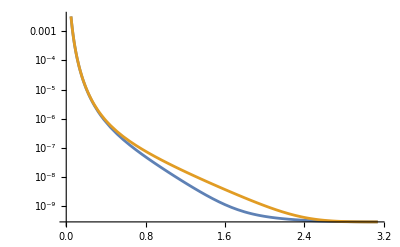

```mathematica
{sm,dσdΩZprime}/.{MZ2->90^2,S->240^2,cw->Sqrt[1-0.231],sw->0.231,Alfa2->1/128^2,Alfa->1/128}/.{MZprime->1000,gZprimeL->1, gZprimeR->0}/.cos->Cos[θ];
LogPlot[%,{θ,0,π}]
```

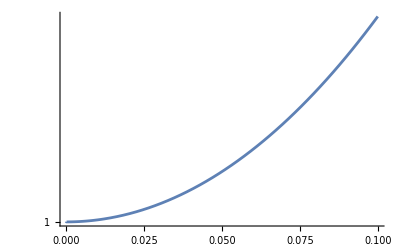

```mathematica
dσdΩZprime/sm/.{MZ2->90^2,S->240^2,cw->Sqrt[1-0.231],sw->0.231,Alfa2->1/128^2,Alfa->1/128}/.{MZprime->1000,gZprimeL->1, gZprimeR->0}/.cos->Cos[θ];
LogPlot[%,{θ,0,0.1}]
```

```mathematica
dσdΩZprime/sm/.{MZ2->90^2,S->240^2,cw->Sqrt[1-0.231],sw->0.231,Alfa2->1/128^2,Alfa->1/128}/.{MZprime->5000}/.cos->Cos[θ];
Manipulate[Plot[%,{θ,0,π}],{gZprimeL,-1,1},{gZprimeR,-1,1}]
```

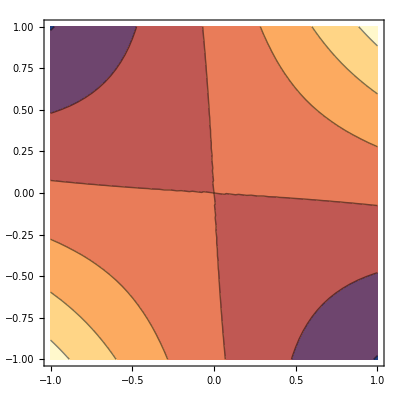

```mathematica
dσdΩZprime/sm/.{MZ2->90^2,S->240^2,cw->Sqrt[1-0.231],sw->0.231,Alfa2->1/128^2,Alfa->1/128}/.{MZprime->5000}/.cos->Cos[θ]/.θ->2;
ContourPlot[%,{gZprimeL,-1,1},{gZprimeR,-1,1}]
```

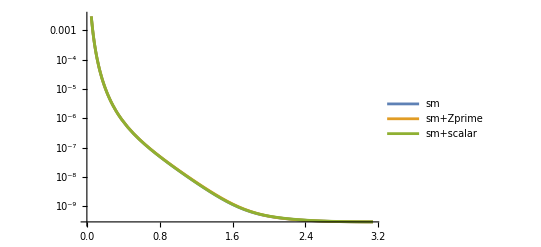

```mathematica
{sm,dσdΩZprime,dσdΩScalar}/.{MZ2->90^2,S->240^2,cw->Sqrt[1-0.231],sw->0.231,Alfa2->1/128^2,Alfa->1/128}/.{MZprime->5000,gZprimeL->1, gZprimeR->0}/.{Mscalar->5000,gNP->1}/.cos->Cos[θ];
LogPlot[%,{θ,0,π},PlotLegends->{"sm","sm+Zprime","sm+scalar"}]
```

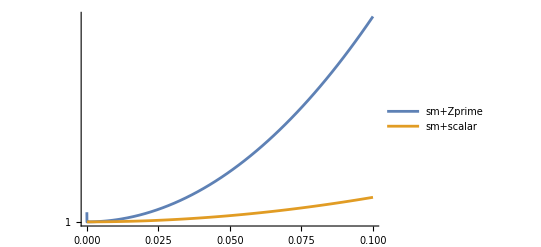

```mathematica
{dσdΩZprime,dσdΩScalar}/sm/.{MZ2->90^2,S->240^2,cw->Sqrt[1-0.231],sw->0.231,Alfa2->1/128^2,Alfa->1/128}/.{MZprime->5000,gZprimeL->1, gZprimeR->0}/.{Mscalar->5000,gNP->1}/.cos->Cos[θ];
LogPlot[%,{θ,0,0.1},PlotLegends->{"sm+Zprime","sm+scalar"}]
```

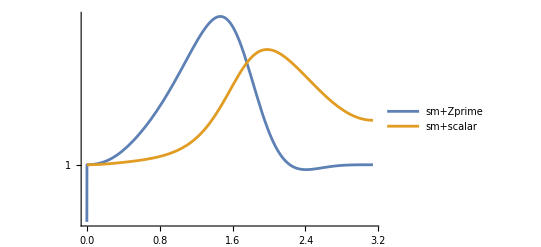

```mathematica
{dσdΩZprime,dσdΩScalar}/sm/.{MZ2->90^2,S->240^2,cw->Sqrt[1-0.231],sw->0.231,Alfa2->1/128^2,Alfa->1/128}/.{MZprime->5000,gZprimeL->1, gZprimeR->0}/.{Mscalar->3500,gNP->1}/.cos->Cos[θ];
LogPlot[%,{θ,0,π},PlotLegends->{"sm+Zprime","sm+scalar"}]
```

## Large angle data generation

### Full statistics

```mathematica
luminosity*dσdΩZprime/.SMnumerics/.BSMnumerics/.cos->Cos[x]/.x->largeAngleBinCentres;
largeAngleExpData=addNoise[#,1/200]&/@%;
```

```mathematica
Table[SetPrecision[{largeAngleBins[[i]],largeAngleBins[[i+1]],largeAngleExpData[[i]]["Value"]*(largeAngleBins[[i+1]]-largeAngleBins[[i]]),largeAngleExpData[[i]]["Uncertainty"]*(largeAngleBins[[i+1]]-largeAngleBins[[i]])},5], {i,1,Length[largeAngleBinCentres]}];
Export["large-angle-data.dat", %,"Table","FieldSeparators"->" ",Alignment->Left]
```

large-angle-data.dat

### Low stats

```mathematica
luminosity*dσdΩZprime/.SMnumerics/.BSMnumerics/.cos->Cos[x]/.x->largeAngleBinCentres;
largeAngleExpDataLowStat=addNoise[#,1/100]&/@%;
```

```mathematica
Table[SetPrecision[{largeAngleBins[[i]],largeAngleBins[[i+1]],largeAngleExpDataLowStat[[i]]["Value"]*(largeAngleBins[[i+1]]-largeAngleBins[[i]]),largeAngleExpDataLowStat[[i]]["Uncertainty"]*(largeAngleBins[[i+1]]-largeAngleBins[[i]])},5], {i,1,Length[largeAngleBinCentres]}];
Export["large-angle-data-low-stats.dat", %,"Table","FieldSeparators"->" ",Alignment->Left]
```

large-angle-data-low-stats.dat

## Check generated data

### Small angle

```mathematica
data = Import["small-angle-data.dat"];
```

```mathematica
sm/.SMnumerics/.cos->Cos[x];
pred=Integrate[%,{x,#[[1]],#[[2]]}]&/@data[[All,1;;2]]/.GeV->1
```

{3.89119×10^-6,3.006×10^-6,2.35876×10^-6,1.87666×10^-6,1.51162×10^-6}

```mathematica
data/. {lower_,upper_,central_,err_}-> {Around[(upper+lower)/2,(upper-lower)/2],Around[central,err]};
{%[[All,1]],%[[All,2]]/pred}//Transpose;
ListPlot[%]
```

-Graphics-

```mathematica
data/. {lower_,upper_,central_,err_}-> {Around[(upper+lower)/2,(upper-lower)/2],Around[central,err]};
%[[All,2]]/pred//Mean
```

3.88150.001810^15

```mathematica
luminosity
```

3.89408×10^15 GeV^2

### Large angle

```mathematica
data = Import["large-angle-data.dat"];
```

```mathematica
convertedData=data/. {lower_,upper_,central_,err_}-> {Around[(upper+lower)/2,(upper-lower)/2],Around[central,err]};
```

```mathematica
luminosity*{sm,dσdΩZprime,dσdΩScalar}/.SMnumerics/.BSMnumerics/.cos->Cos[x]//Simplify;
pred=NIntegrate[%,{x,#[[1]],#[[2]]}]&/@data[[All,1;;2]];
pred=Transpose[{convertedData[[All,1]],#}]&/@(pred//Transpose);
```

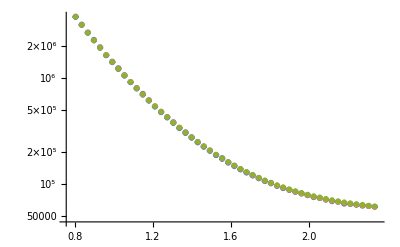

```mathematica
Show[
ListLogPlot[convertedData],
ListLogPlot[pred]
]
```

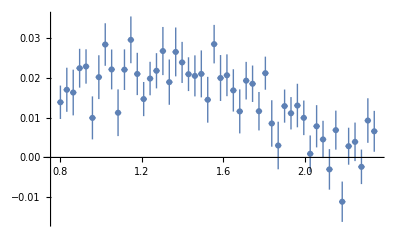

```mathematica
{convertedData[[All,1]],convertedData[[All,2]]/pred[[1,All,2]]-1}//Transpose;
ListPlot[%]
```

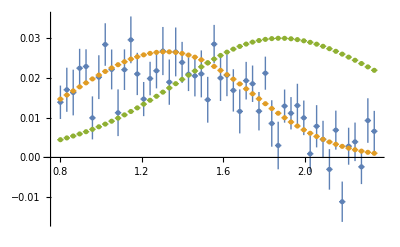

```mathematica
{convertedData[[All,2]]/pred[[1,All,2]],pred[[2,All,2]]/pred[[1,All,2]],pred[[3,All,2]]/pred[[1,All,2]]}-1;
Transpose[{convertedData[[All,1]],#}]&/@%;
ListPlot[%]
```